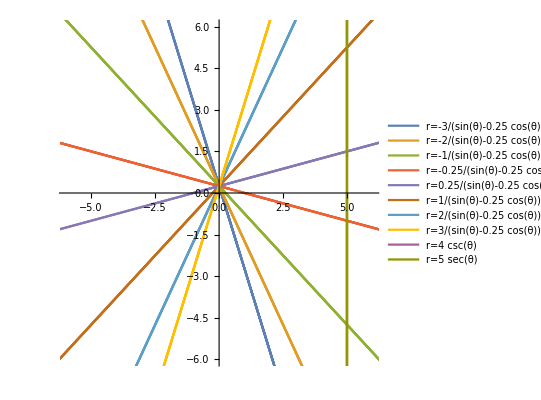

```mathematica
den[m_,b_]:=b/(Sin[t] - m Cos[t]);
PolarPlot[{den[-3,0.25],den[-2,0.25],den[-1,0.25],den[-0.25,0.25],den[0.25,0.25],den[1,0.25],den[2,0.25],den[3,0.25],4Csc[t],5Sec[t]},{t,0.25,2Pi},PlotRange->{{-6,6},{-6,6}},PlotLegends->{Row[{"r=",TraditionalForm[-3/(Sin[θ]-0.25Cos[θ])]}], Row[{"r=",TraditionalForm[-2/(Sin[θ]-0.25Cos[θ])]}], Row[{"r=",TraditionalForm[-1/(Sin[θ]-0.25Cos[θ])]}],Row[{"r=",TraditionalForm[-0.25/(Sin[θ]-0.25Cos[θ])]}], Row[{"r=",TraditionalForm[0.25/(Sin[θ]-0.25Cos[θ])]}],Row[{"r=",TraditionalForm[1/(Sin[θ]-0.25Cos[θ])]}], Row[{"r=",TraditionalForm[2/(Sin[θ]-0.25Cos[θ])]}], Row[{"r=",TraditionalForm[3/(Sin[θ]-0.25Cos[θ])]}],Row[{"r=",TraditionalForm[4Csc[θ]]}],Row[{"r=",TraditionalForm[5 Sec[θ]]}]}]
```

```mathematica
TraditionalForm[1/2]
```

1/2

```mathematica
y=mx;
r Sin[t] = m r Cos[t];
r(Sin[t]-m Cos[t])=0
```

```mathematica
y=m x
y/x = m
```

```mathematica
?PolarPlot
```

PolarPlot[r,{θ,θ_min,θ_max}] generates a polar plot of a curve with radius r as a function of angle θ.
PolarPlot[{f_1,f_2,…},{θ,θ_min,θ_max}] makes a polar plot of curves with radius functions f_1, f_2, ….

```mathematica
PolarPlot[0,{θ,0,1},Epilog->Line[{Scaled[{1,4}],Scaled[{0,0}]}]]
```

-Graphics-

```mathematica
PolarParametricPlot[{rT:{_,_}..}|rT2:{_,_},uv:{_,_,_}..,opts:OptionsPattern[]]:=ParametricPlot[Evaluate[# {Cos@#2,Sin@#2}&@@@{rT}],uv,opts]
```

```mathematica
PolarParametricPlot[{t,45 Degree},{t,-10,10}]
```

ParametricPlot::write: Tag ArcTan in ArcTan[3] is Protected.

ParametricPlot[{{ArcTan[3]/(√2),ArcTan[3]/(√2)}},{ArcTan[3],-10,10}]

```mathematica
Show[
PolarPlot[0,{t,0,2Pi},PlotRange->{{-6,6},{-6,6}}],
Graphics[Rotate[Line[500 {{-1,0},{1,0}}],Pi/6]]
]
```

-Graphics-

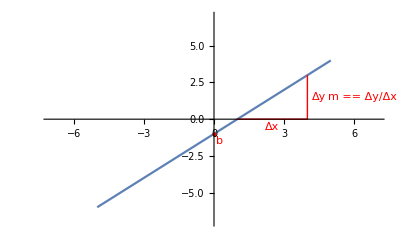

```mathematica
Plot[x-1,{x,-5,5},PlotRange->{{-7,7},{-7,7}},Ticks -> None, Epilog->{Red,PointSize[Large],Point[{0,-1}],Line[{{1,0},{4,0},{4,3}}],Text[b,{0.25,-1.5}],Text[Δy,{4.5,1.5}],Text[Δx,{2.5,-0.5}],Text[Row[{"m == ",TraditionalForm[Δy/Δx]}],{6.375,1.5}]}]
```

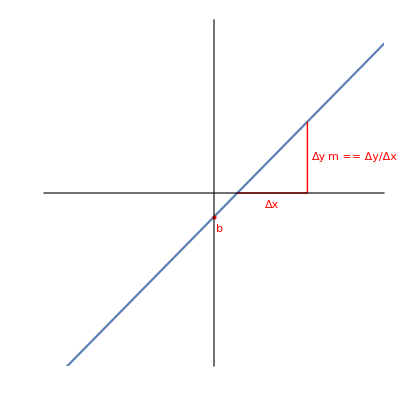

```mathematica
ParametricPlot[{3t,3t-1},{t,-3,3},PlotRange->{{-7,7},{-7,7}},Ticks->None,Epilog->{Red,PointSize[Large],Point[{0,-1}],Line[{{1,0},{4,0},{4,3}}],Text[b,{0.25,-1.5}],Text[Δy,{4.5,1.5}],Text[Δx,{2.5,-0.5}],Text[Row[{"m == ",TraditionalForm[Δy/Δx]}],{6.375,1.5}]}]
```

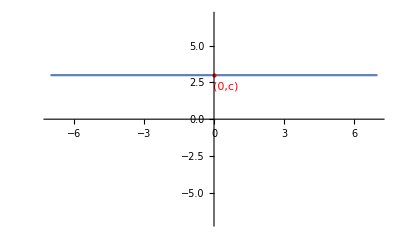

```mathematica
Plot[3,{x,-7,7},PlotRange->{{-7,7},{-7,7}},Ticks -> None,Epilog->{Red,PointSize[Large],Point[{0,3}],Text["(0,c)",{0.5,2.25}]}]
```

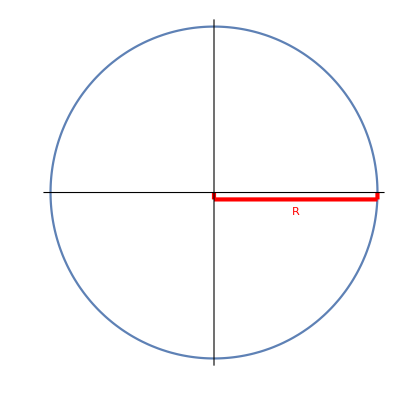

```mathematica
ParametricPlot[{3Cos[t],3Sin[t]},{t,0,2Pi},Ticks->None,Epilog->{Red,Thickness[0.0075],Line[{{0,-0.125},{0,0}}], Line[{{0,-0.125},{3,-0.125}}],Line[{{3,-0.125},{3,0}}],Text[R,{1.5,-0.35}]}]
```

```mathematica
?Line
```

Line[{p_1,p_2,…}] represents the line segments joining a sequence for points p_i.
Line[{{p_11,p_12,…},{p_21,…},…}] represents a collection of lines.

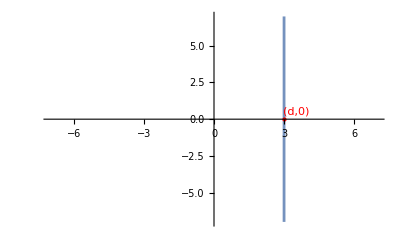

```mathematica
Plot[0,{x,-7,7},PlotStyle->{Transparent},Ticks->None,PlotRange->{{-7,7},{-7,7}},Epilog->{RGBColor[117/256,147/256,191/256,1],Thickness[0.005],Line[{{3,-7},{3,7}}],Red,PointSize[Large],Point[{3,0}],Text["(d,0)",{3.5,0.5}]}]
```

```mathematica
RGBColor[117/256,147/256,191/256,1]
```

RGBColor[Rational[117, 256], Rational[147, 256], Rational[191, 256], 1]

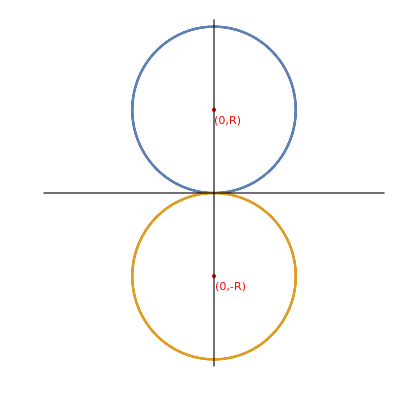

```mathematica
PolarPlot[{6Sin[t],-6Sin[t]},{t,0,2Pi},PlotRange->{{-6,6},{-6,6}},Ticks->None,Epilog->{Red,PointSize[Large],Point[{{0,3},{0,-3}}],Text["(0,R)",{0.5,2.625}],Text["(0,-R)",{0.61,-3.375}]}]
```

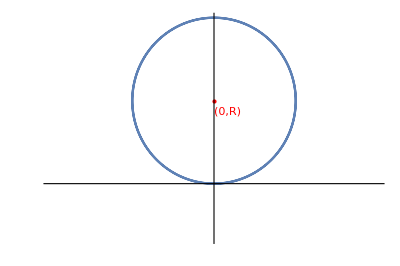

```mathematica
PolarPlot[6Sin[t],{t,0,2Pi},PlotRange->{{-6,6},{-2,6}},Ticks->None,Epilog->{Red,PointSize[Large],Point[{0,3}],Text["(0,R)",{0.5,2.625}]}]
```

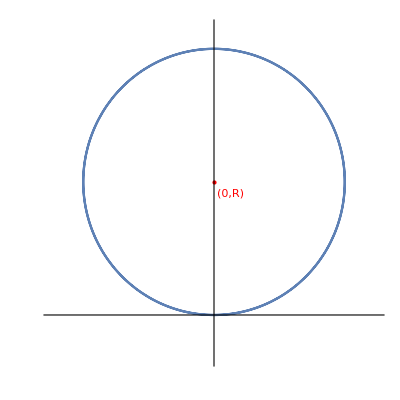

```mathematica
ParametricPlot[{6Sin[t]Cos[t],6Sin[t]Sin[t]},{t,0,2Pi},PlotRange->{{-3.75,3.75},{-1,6.5}},Ticks->None, Epilog->{Red,PointSize[Large],Point[{0,3}],Text["(0,R)",{0.375,2.75}]}](*,Text[Style[Row[{TraditionalForm[R<0]," is below the ",TraditionalForm[x],"-axis"}],Bold,16,FontFamily->"Times",Background->White],{0,-1.5}]}]*)
```

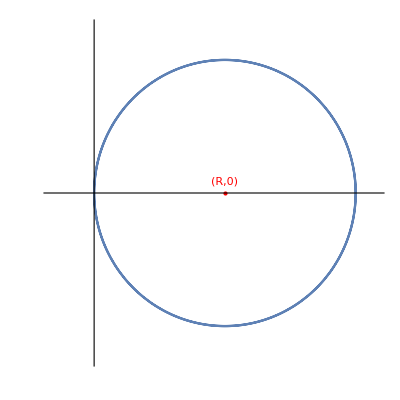

```mathematica
ParametricPlot[{6Cos[t]Cos[t],6Cos[t]Sin[t]},{t,0,2Pi},PlotRange->{{-1,6.5},{-3.75,3.75}},Ticks->None, Epilog->{Red,PointSize[Large],Point[{3,0}],Text["(R,0)",{3,0.25}]}](*,Text[Style[Row[{TraditionalForm[R<0]," is left of the ",TraditionalForm[y],"-axis"}],Bold,16,FontFamily->"Times",Background->White],{2.25,-3.75}]}]*)
```

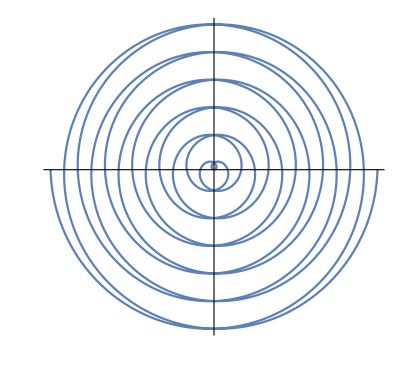

```mathematica
PolarPlot[t,{t,-12Pi,12Pi},PlotRange->Automatic,Ticks->None]
```

```mathematica
Exp[6.28]//N
```

533.789

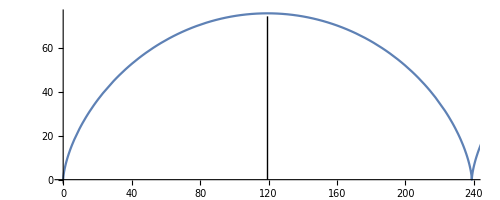

```mathematica
r=38;
ParametricPlot[{r(t-Sin[t]),r(1-Cos[t])},{t,0,r Pi},PlotRange->{{0,2 r Pi},Automatic},(*Ticks->{{2Pi,4Pi,6Pi,8Pi,10Pi,12Pi,14Pi,16Pi},None},*)Epilog->{Line[{{r Pi,0},{r Pi,(5 r / 8)Pi}}]}](*Epilog->{Line[{{0,5Pi/4},{50,5Pi/4}}]}]*)
```

```mathematica
1->0.625
2->1.25
4->2.5
8->5
```

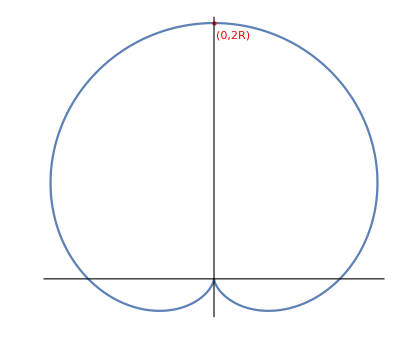

```mathematica
PolarPlot[2(1+Sin[t]),{t,0,2Pi},Ticks->None,Epilog->{Red,PointSize[Large],,Point[{0,4}],FontSize->12,Text["(0,2R)",{0.3,3.8}]}]
```

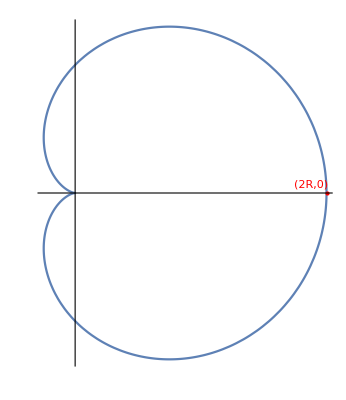

```mathematica
PolarPlot[2(1+Cos[t]),{t,0,2Pi},Ticks->None,Epilog->{Red,PointSize[Large],Point[{4,0}],FontSize->12,Text["(2R,0)",{3.75,0.125}]}]
```

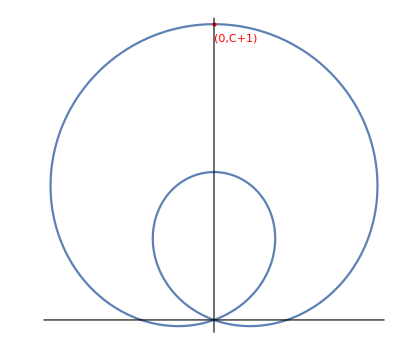

```mathematica
PolarPlot[1+3Sin[t],{t,0,2Pi},Ticks->None,Epilog->{Red,PointSize[Large],Point[{0,4}],FontSize->12,Text["(0,C+1)",{0.3,3.8}]}]
```

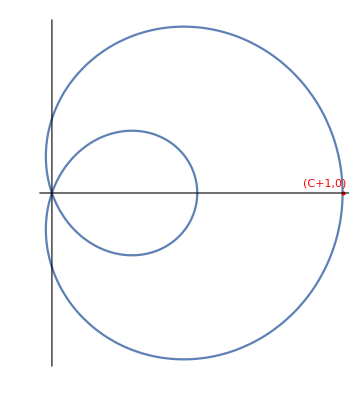

```mathematica
PolarPlot[1+3Cos[t],{t,0,2Pi},Ticks->None,Epilog->{Red,PointSize[Large],Point[{4,0}],FontSize->12,Text["(C+1,0)",{3.75,0.125}]}]
```

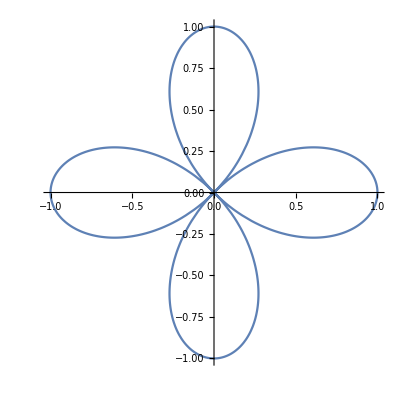

```mathematica
PolarPlot[{Cos[2t]},{t,0,2Pi}]
```

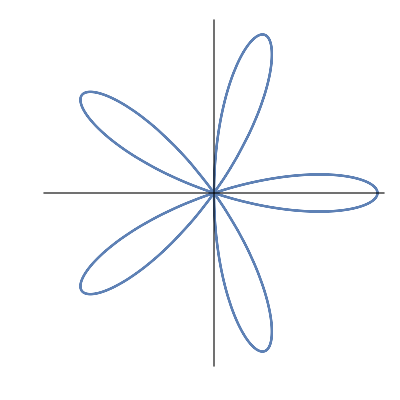

```mathematica
PolarPlot[Cos[5t],{t,0,2Pi},Ticks->None,PlotRange->{{-1,1},{-1,1}}]
```